```mathematica
allfiles=GetAllSZDailyFiles[];
```

```mathematica
prefit=0;prefitlist={};getstock={};

Dynamic[prefit]
(
num=#;
data=BinaryReadList[allfiles[[#]],{"Integer32","Integer32","Integer32","Integer32","Integer32","Real32","Integer32","Integer32"}];
data[[All,6]]=IntegerPart[data[[All,6]]];
newdata=Join[data,KDJ[data[[All,{2,3,4,5}]],9],2];
(If[#[[1,-2]]<10,prefit=prefit+#[[-1,5]]-#[[1,5]]-10;AppendTo[prefitlist,prefit]])&/@Partition[If[Length[newdata]<250,newdata,newdata[[-250;;-1]]],10,1];
If[newdata[[-1,-2]]<10,AppendTo[getstock,allfiles[[#]]]]
)&/@Range[1,500];
getstock
```

{/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz000156.day,/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz000806.day,/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz000820.day,/home/math/.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002012.day}

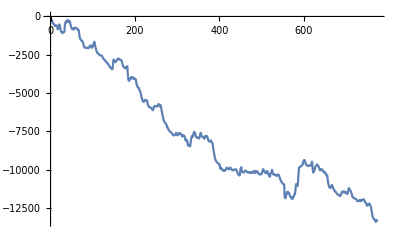

```mathematica
ListLinePlot[prefitlist]
```

```mathematica
allfiles[[1200;;1300]]
```

{.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002740.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002741.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002742.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002743.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002745.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002746.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002747.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002748.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002749.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002750.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002751.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002752.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002753.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002755.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002756.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002757.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002758.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002759.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002760.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002761.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002762.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002763.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002765.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002766.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002767.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002768.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002769.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002770.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002771.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002772.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002773.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002774.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002775.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002776.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002777.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002778.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002779.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002780.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002781.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002782.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002783.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002785.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002786.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002787.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002788.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002789.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002790.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002791.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002792.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002793.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002795.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002796.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002797.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002798.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002799.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002800.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002801.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002802.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002803.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002805.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002806.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002807.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002808.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002809.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002810.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002811.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002812.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002813.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002815.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002816.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002817.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002818.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002819.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002820.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002821.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002822.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002823.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002824.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002825.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002826.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002827.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002828.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002829.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002830.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002831.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002832.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002833.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002835.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002836.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002837.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002838.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002839.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002840.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002841.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002842.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002843.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002845.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002846.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002847.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002848.day,.wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/sz002849.day}